## The Repressilator

xCellerator implementation 
Created: 13 August 2005 BES
Revised: 12 Nov 2012 for new version of xlr8r hill reaction

Reference: Elowitz MB, Leibler S (2000) A synthetic oscillatory network of transcriptional regulators. Nature. 403:335-338.

```mathematica
<<xlr8r.m
```

xCellerator 0.92 (11-Nov-2012) loaded Tue 23 Apr 2013 12:59:52
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

### Variable Associations:

X = lacl mRNA
Y = tetR mRNA
Z = cl mRNA

PX = lacl Protein 
PY = tetR Protein
PZ = cl Protein

```mathematica
repressilator={
{PZ↦X,hill[α1,n,K,0,1,α]},
{PX↦Y,hill[α1,n,K,0,1,α]},
{PY↦Z,hill[α1,n,K,0,1,α]},
{X⇄∅,k1,α0},{Y⇄∅,k1,α0},{Z⇄∅,k1,α0},
{PX⇄∅,β, β*X[t]},{PY⇄∅,β, β*Y[t]},{PZ⇄∅,β,β *Z[t]}

};
```

```mathematica
ODE[repressilator]//TableForm
```

PX'[t]==-β PX[t]+β X[t]
PY'[t]==-β PY[t]+β Y[t]
PZ'[t]==-β PZ[t]+β Z[t]
X'[t]==α0+α/(K^n+PZ[t]^n)+(α1 PZ[t]^n)/(K^n+PZ[t]^n)-k1 X[t]
Y'[t]==α0+α/(K^n+PX[t]^n)+(α1 PX[t]^n)/(K^n+PX[t]^n)-k1 Y[t]
Z'[t]==α0+α/(K^n+PY[t]^n)+(α1 PY[t]^n)/(K^n+PY[t]^n)-k1 Z[t]

```mathematica
repressilatorRates={α->250,α0->0,α1->0,β->5,n->2.1,k1-> 1,K-> 1};
```

```mathematica
repressilatorIC={PX-> 5, PZ-> 15};
```

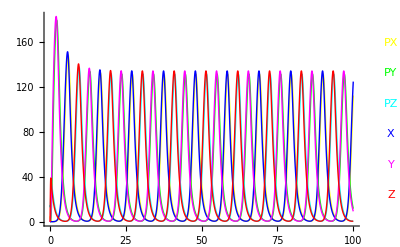

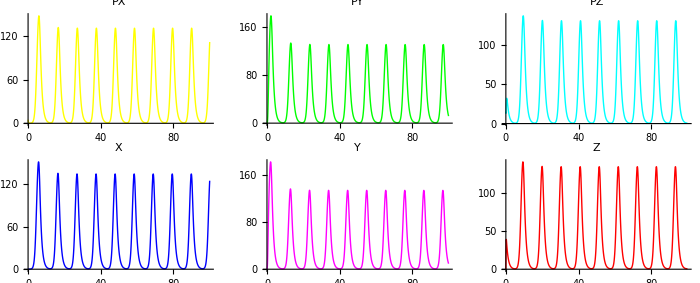

{{PX→InterpolatingFunction[{{0.,100.}},<>],PY→InterpolatingFunction[{{0.,100.}},<>],PZ→InterpolatingFunction[{{0.,100.}},<>],X→InterpolatingFunction[{{0.,100.}},<>],Y→InterpolatingFunction[{{0.,100.}},<>],Z→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
sim=run[repressilator, 
timeSpan-> 100,
rates-> repressilatorRates,
initialConditions-> repressilatorIC,ImageSize-> 700,
plotVariables-> All,plot-> True,gridPlotVariables-> All,
MaxSteps-> 25000]
```